```mathematica
lista1 = {
{1.8,7.1},{2.3,8.0},{2.8,9.0},{3.3,9.9}
}
```

{{1.8,7.1},{2.3,8.},{2.8,9.},{3.3,9.9}}

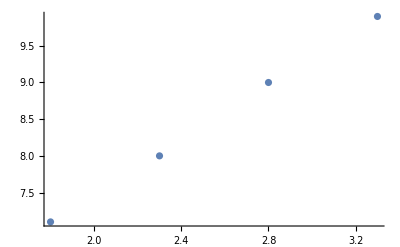

```mathematica
ListPlot[lista1]
```

```mathematica
t[p_]=Fit[lista1,{1,p},p]
```

3.706+1.88 p

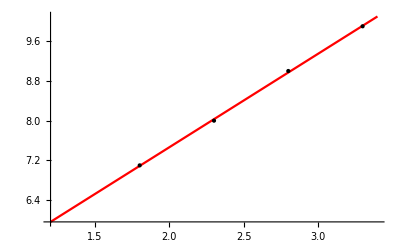

```mathematica
Plot[ t[p], {p,1.2, 3.4}, PlotStyle->Red, Epilog-> Map[Point, lista1]]
```

```mathematica
t[1.4]
```

6.338